```mathematica
SetDirectory["C:\\Users\\Andrey\\Documents\\Deliveries"]
```

C:\Users\Andrey\Documents\Deliveries

```mathematica
d=Import["sales.csv"]
```

{{,S1,,S2,,S3,,S4,,S5,,S6,,S7,,S8,,S9,,S10,,S11,,S12,,S13,,S14,,S15,,S16,,S17,,S18,,S19,,S20,},{daily sale,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2,P1,P2},364,{12/31/2015,0,3,0,1,0,12,0,1,0,7,0,1,0,20,0,18,0,35,0,23,0,4,0,22,0,3,0,5,0,24,0,0,0,19,0,0,0,5,0,18}}
 |  |  |  |

```mathematica
{7,1}.#&/@{{2,6},{10,6},{3,5},{5,5},{8,5},{0,4},{2,3},{6,3},{10,3},{12,3},{1,2},{4,2},{11,2},{3,1},{8,1},{10,1},{2,0},{4,0},{7,0},{12,0},{4,3},{9,2}}
```

{20,76,26,40,61,4,17,45,73,87,9,30,79,22,57,71,14,28,49,84,31,65}

```mathematica
MatrixForm@Partition[Max/@(d⟦%18,2;;⟧ᵀ),2]
```

(15 | 13
14 | 15
19 | 20
19 | 20
15 | 15
20 | 20
28 | 30
29 | 29
35 | 35
24 | 25
29 | 28
29 | 28
29 | 30
34 | 34
30 | 29
39 | 38
24 | 24
20 | 18
14 | 15
19 | 19)

```mathematica
Export["monthly_sales.csv",Total[SplitBy[SortBy[d,FromDigits@If[#⟦1⟧==""∨#⟦1⟧=="daily sale","",StringSplit[#⟦1⟧,"/"]⟦1⟧]&],If[#⟦1⟧==""∨#⟦1⟧=="daily sale","",FromDigits@StringSplit[#⟦1⟧,"/"]⟦1⟧]&]⟦2;;,;;,2;;⟧,{2}]]
```

monthly_sales.csv

```mathematica
Max[{181,0,150,0,228,0,254,0,167,0,254,0,305,0,389,0,469,0,288,0,415,0,364,0,421,0,410,0,463,0,449,0,352,0,251,0,199,0,217,0}⟦;;;;2⟧/26.]
```

18.0385

```mathematica
Max[{0,168,0,233,0,288,0,274,0,192,0,276,0,353,0,409,0,382,0,349,0,336,0,365,0,389,0,488,0,408,0,542,0,360,0,208,0,204,0,275
}⟦2;;;;2⟧/27.]
```

20.0741

```mathematica
1.Mean@Flatten@d⟦#;;;;7,2;;;;2⟧&/@{7,8,9,3,4,5}
```

{7.94519,7.81923,8.00673,7.83962,7.48654,7.87404}

```mathematica
1.Mean@Flatten@d⟦#;;;;7,3;;;;2⟧&/@{7,8,9,3,4,5}
```

{4.17885,4.47404,4.72692,4.60943,4.47212,4.4125}

```mathematica
1.{Mean@%17,StandardDeviation@%17}
```

{7.82856,0.181441}

```mathematica
1.{Mean@%18,StandardDeviation@%18}
```

{4.47898,0.186046}

```mathematica
{Abs@((%17-%21⟦1⟧)/(%21⟦2⟧)),Abs@((%18-%20⟦1⟧)/(%20⟦2⟧))}
```

{{0.642817,0.0514114,0.981982,0.060977,1.88502,0.250657},{1.6132,0.0265403,1.33272,0.701213,0.0368769,0.357311}}

```mathematica
Integrate[ⅇ^(-x^2),{x,-1.8850218958457097(√2)/2,1.8850218958457097(√2)/2}]/(√π)
```

0.940573

```mathematica
avg # of cust so far this month
past / days in that month
```

```mathematica
exp * k
```

```mathematica
1) "traveling salesman"
```

```mathematica
2)a)run for a while
b)get average
c)make a histogram with 313*20*2 bins
d)
```

```mathematica
Mean@{17407613.76,17395292.,17416721.44,17409393.04,17379072.56,17431165.68,17387615.28,17408274.72,17418568.08,17403856.88,17405828.8,17360475.36,17395775.12,17388004.48,17426911.36,17418027.52,17419513.84,17404243.84,17398666.,17402569.04}
```

1.74039×10^7

```mathematica
Mean@{17392003.36,17426987.44000001,17407146.,17375950.16,17395081.84,17373079.36000001,17412358.8,17386110.72000001,17373776.48,17402551.2,17407074.8,17401355.92000001,17400922.48,17395235.68000001,17406752.16,17382277.04,17427902.40000001,17378959.76,17411346.8,17390460.48}
```

1.73974×10^7

```mathematica
Mean@{17401332.240000006,17404777.2,17377516.4,17411636.640000004,17389248.560000002,17418429.280000005,17396341.360000003,17400996.32,17379718.720000006,17392363.680000003,17405226.640000004,17441263.12,17392439.76,17412480.880000003,17383551.2,17373167.92,17419571.360000007,17425696.8,17420624.8,17397778.160000004}
```

1.74022×10^7

```mathematica
Mean@{17425029.92,
17358416.96,
17431022.000000004,
17392735.84,
17394342.400000002,
17421839.200000003,
17386692.4,
17421708.800000004,
17355249.200000003,
17410239.200000003,
17387856.720000006,
17435298.720000006,
17421992.080000006,
17400174.160000004,
17422100.240000002,
17404142.48,
17391919.840000004,
17418531.440000005,
17400382.320000004,
17353847.520000003}
```

1.74017×10^7

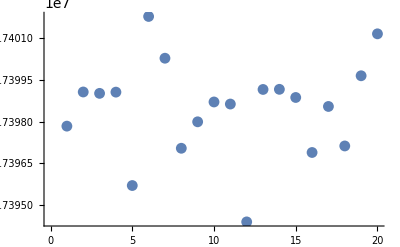

```mathematica
ListPlot@{17397839.360000003,
17399070.160000004,
17399020.560000006,
17399065.040000003,
17395698.560000002,
17401792.160000004,
17400286.880000003,
17397041.840000004,
17397995.200000007,
17398710.32,
17398635.520000003,
17394388.000000004,
17399161.44,
17399166.16,
17398872.160000004,
17396889.520000003,
17398548.400000002,
17397124.96,
17399654.64,
17401166.240000002}
```

traveling salesman
warehouse restocking on 1schedule

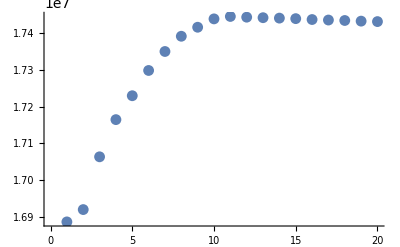

```mathematica
ListPlot@{16885698.000000004,
16919309.200000003,
17063199.6,
17164610.800000004,
17229763.6,
17298659.6,
17350424.400000002,
17391982.000000004,
17416552.400000002,
17439360.400000002,
17445962.000000004,
17444003.6,
17442597.200000003,
17441435.6,
17440019.6,
17437598.000000004,
17436208.400000002,
17434974.8,
17433206.0,
17431970.0
}
```

```mathematica
?StringReplace
```

StringReplace[string,s→sp] or StringReplace[string,{s_1→sp_1,s_2→sp_2,…}] replaces the string expressions s_i by sp_i whenever they appear as substrings of "string". 
StringReplace[string,srules,n] does only the first n replacements. 
StringReplace[{s_1,s_2,…},srules] gives the list of results for each of the s_i.

```mathematica
Total@Partition[Partition[ToExpression@StringReplace["{0 0.0 16798574.000000004
0 0.2 16959011.6
0 0.4 17124582.000000004
0 0.6 17267904.400000002
0 0.8 17349226.000000004
0 1.0 17401674.000000004
0 1.2 17427854.800000004
0 1.4 17434286.000000004
0 1.6 17434488.400000002
0 1.8 17433178.000000004
0 2.0 17431770.0
0 2.2 17429511.6
0 2.4 17427847.6
0 2.6 17425971.599999998
0 2.8 17424442.8
0 3.0 17423010.0
0 3.2 17421664.4
0 3.4 17420231.599999998
0 3.6 17419038.799999997
0 3.8 17418023.599999998
1 0.0 16810910.000000004
1 0.2 16968156.400000002
1 0.4 17143110.800000004
1 0.6 17268302.000000004
1 0.8 17349674.800000004
1 1.0 17395604.400000002
1 1.2 17426778.000000004
1 1.4 17433556.400000002
1 1.6 17435994.000000004
1 1.8 17434670.8
1 2.0 17432227.6
1 2.2 17429868.400000002
1 2.4 17428857.2
1 2.6 17427211.6
1 2.8 17425382.0
1 3.0 17424030.799999997
1 3.2 17422293.2
1 3.4 17420953.999999996
1 3.6 17419655.599999998
1 3.8 17418784.4
2 0.0 16806693.200000003
2 0.2 16969310.800000004
2 0.4 17120075.6
2 0.6 17269602.800000004
2 0.8 17354355.6
2 1.0 17400442.800000004
2 1.2 17424561.200000003
2 1.4 17434988.400000002
2 1.6 17434558.800000004
2 1.8 17433922.000000004
2 2.0 17432219.6
2 2.2 17430429.2
2 2.4 17428473.2
2 2.6 17427112.4
2 2.8 17425506.8
2 3.0 17424136.4
2 3.2 17422770.799999997
2 3.4 17421333.2
2 3.6 17420147.599999998
2 3.8 17419060.4
3 0.0 16803007.6
3 0.2 16953082.800000004
3 0.4 17123860.400000002
3 0.6 17264338.800000004
3 0.8 17344220.400000002
3 1.0 17397029.200000003
3 1.2 17418999.6
3 1.4 17432251.6
3 1.6 17435197.200000003
3 1.8 17434100.400000002
3 2.0 17431806.0
3 2.2 17430666.8
3 2.4 17428706.0
3 2.6 17427409.2
3 2.8 17425754.0
3 3.0 17424413.2
3 3.2 17422629.2
3 3.4 17421472.4
3 3.6 17420393.2
3 3.8 17419435.599999998
4 0.0 16816666.800000004
4 0.2 16987408.400000002
4 0.4 17135958.000000004
4 0.6 17264918.800000004
4 0.8 17345113.200000003
4 1.0 17396030.800000004
4 1.2 17425646.800000004
4 1.4 17434334.800000004
4 1.6 17436220.400000002
4 1.8 17435106.8
4 2.0 17432305.200000003
4 2.2 17429719.6
4 2.4 17428066.0
4 2.6 17426615.6
4 2.8 17424962.0
4 3.0 17423404.4
4 3.2 17422322.0
4 3.4 17421023.599999998
4 3.6 17419777.999999996
4 3.8 17418817.999999996
5 0.0 16816011.6
5 0.2 16994063.6
5 0.4 17146043.6
5 0.6 17246605.200000003
5 0.8 17343635.6
5 1.0 17403976.400000002
5 1.2 17421550.800000004
5 1.4 17433723.6
5 1.6 17436242.000000004
5 1.8 17434422.000000004
5 2.0 17432031.6
5 2.2 17430237.2
5 2.4 17429457.2
5 2.6 17427762.8
5 2.8 17425996.4
5 3.0 17424510.799999997
5 3.2 17423133.2
5 3.4 17421878.0
5 3.6 17420622.799999997
5 3.8 17419499.599999998
6 0.0 16811159.6
6 0.2 16966116.400000002
6 0.4 17143881.200000003
6 0.6 17267376.400000002
6 0.8 17352158.800000004
6 1.0 17406414.800000004
6 1.2 17427091.6
6 1.4 17432620.400000002
6 1.6 17433374.800000004
6 1.8 17433452.400000002
6 2.0 17431412.400000002
6 2.2 17429076.400000002
6 2.4 17427239.6
6 2.6 17426097.2
6 2.8 17424714.8
6 3.0 17423099.599999998
6 3.2 17421958.0
6 3.4 17420663.599999998
6 3.6 17419345.999999996
6 3.8 17418246.799999997
7 0.0 16807766.800000004
7 0.2 16962702.000000004
7 0.4 17145712.400000002
7 0.6 17250746.000000004
7 0.8 17336682.000000004
7 1.0 17390590.000000004
7 1.2 17421840.400000002
7 1.4 17435005.200000003
7 1.6 17437019.6
7 1.8 17435011.6
7 2.0 17433418.0
7 2.2 17431125.2
7 2.4 17429394.8
7 2.6 17427635.6
7 2.8 17426135.599999998
7 3.0 17424453.2
7 3.2 17423212.4
7 3.4 17421830.0
7 3.6 17420569.999999996
7 3.8 17419542.799999997
8 0.0 16814723.6
8 0.2 16958911.6
8 0.4 17141112.400000002
8 0.6 17260336.400000002
8 0.8 17345358.800000004
8 1.0 17403459.6
8 1.2 17424330.800000004
8 1.4 17433274.800000004
8 1.6 17434569.200000003
8 1.8 17434669.200000003
8 2.0 17433089.200000003
8 2.2 17430773.2
8 2.4 17428932.4
8 2.6 17427328.4
8 2.8 17425617.2
8 3.0 17424206.0
8 3.2 17422761.2
8 3.4 17421491.599999998
8 3.6 17420341.999999996
8 3.8 17419398.799999997
9 0.0 16807983.6
9 0.2 16953492.400000002
9 0.4 17130084.400000002
9 0.6 17254058.000000004
9 0.8 17341142.800000004
9 1.0 17391382.800000004
9 1.2 17426330.000000004
9 1.4 17435164.400000002
9 1.6 17436849.200000003
9 1.8 17435152.400000002
9 2.0 17432414.0
9 2.2 17430309.2
9 2.4 17428705.2
9 2.6 17427067.6
9 2.8 17425581.2
9 3.0 17423902.0
9 3.2 17422481.2
9 3.4 17421352.4
9 3.6 17420142.799999997
9 3.8 17418985.999999996
10 0.0 16796519.6
10 0.2 16965258.800000004
10 0.4 17136019.6
10 0.6 17265019.6
10 0.8 17348674.800000004
10 1.0 17396242.000000004
10 1.2 17425226.000000004
10 1.4 17432948.400000002
10 1.6 17436214.000000004
10 1.8 17434178.000000004
10 2.0 17431966.0
10 2.2 17430668.400000002
10 2.4 17428600.4
10 2.6 17426802.8
10 2.8 17425566.8
10 3.0 17423790.799999997
10 3.2 17422701.2
10 3.4 17421151.599999998
10 3.6 17420127.599999998
10 3.8 17419050.799999997
11 0.0 16799610.000000004
11 0.2 16959821.200000003
11 0.4 17136407.6
11 0.6 17260908.400000002
11 0.8 17342681.200000003
11 1.0 17396609.200000003
11 1.2 17420635.6
11 1.4 17432244.400000002
11 1.6 17435362.000000004
11 1.8 17433845.200000003
11 2.0 17432944.400000002
11 2.2 17430659.6
11 2.4 17428828.4
11 2.6 17427102.8
11 2.8 17425614.8
11 3.0 17423975.599999998
11 3.2 17422715.599999998
11 3.4 17421494.0
11 3.6 17420176.4
11 3.8 17419151.599999998
12 0.0 16837373.200000003
12 0.2 16974346.800000004
12 0.4 17147316.400000002
12 0.6 17267166.800000004
12 0.8 17350649.200000003
12 1.0 17400782.800000004
12 1.2 17429413.200000003
12 1.4 17434491.6
12 1.6 17432811.6
12 1.8 17432571.6
12 2.0 17432099.6
12 2.2 17429895.6
12 2.4 17428362.0
12 2.6 17426856.4
12 2.8 17425163.599999998
12 3.0 17423774.0
12 3.2 17422418.0
12 3.4 17420937.2
12 3.6 17419545.2
12 3.8 17418489.2
13 0.0 16808709.200000003
13 0.2 16943138.000000004
13 0.4 17139281.200000003
13 0.6 17259502.800000004
13 0.8 17352214.800000004
13 1.0 17403785.200000003
13 1.2 17425414.000000004
13 1.4 17434774.800000004
13 1.6 17435879.6
13 1.8 17433876.400000002
13 2.0 17432891.6
13 2.2 17431241.2
13 2.4 17429158.0
13 2.6 17427473.2
13 2.8 17425944.4
13 3.0 17424510.799999997
13 3.2 17423135.599999998
13 3.4 17421770.0
13 3.6 17420665.999999996
13 3.8 17419494.799999997
14 0.0 16789488.400000002
14 0.2 16951654.800000004
14 0.4 17127934.000000004
14 0.6 17249895.6
14 0.8 17345259.6
14 1.0 17395354.800000004
14 1.2 17424897.200000003
14 1.4 17433834.000000004
14 1.6 17437176.400000002
14 1.8 17435341.200000003
14 2.0 17432580.400000002
14 2.2 17430508.400000002
14 2.4 17428430.0
14 2.6 17426788.4
14 2.8 17425336.4
14 3.0 17423975.599999998
14 3.2 17422427.599999998
14 3.4 17421059.599999998
14 3.6 17419840.4
14 3.8 17418837.2
15 0.0 16798743.6
15 0.2 16935540.400000002
15 0.4 17133286.000000004
15 0.6 17251286.800000004
15 0.8 17344500.400000002
15 1.0 17391080.400000002
15 1.2 17422342.800000004
15 1.4 17432608.400000002
15 1.6 17434742.000000004
15 1.8 17434229.200000003
15 2.0 17431777.200000003
15 2.2 17429758.0
15 2.4 17428082.0
15 2.6 17427006.8
15 2.8 17425066.8
15 3.0 17423511.599999998
15 3.2 17422326.799999997
15 3.4 17421071.599999998
15 3.6 17419794.799999997
15 3.8 17418873.2
16 0.0 16766519.600000003
16 0.2 16931664.400000002
16 0.4 17122286.800000004
16 0.6 17263870.000000004
16 0.8 17350680.400000002
16 1.0 17402110.800000004
16 1.2 17424435.6
16 1.4 17436312.400000002
16 1.6 17435817.200000003
16 1.8 17434575.6
16 2.0 17432590.0
16 2.2 17430250.8
16 2.4 17429044.4
16 2.6 17427400.4
16 2.8 17425962.0
16 3.0 17424333.2
16 3.2 17423067.599999998
16 3.4 17421634.799999997
16 3.6 17420429.999999996
16 3.8 17419253.999999996
17 0.0 16802059.6
17 0.2 16987472.400000002
17 0.4 17143714.800000004
17 0.6 17277215.6
17 0.8 17357580.400000002
17 1.0 17399995.6
17 1.2 17424993.200000003
17 1.4 17433247.6
17 1.6 17434994.000000004
17 1.8 17434537.200000003
17 2.0 17432706.8
17 2.2 17430370.0
17 2.4 17428413.2
17 2.6 17427166.0
17 2.8 17425493.2
17 3.0 17423971.599999998
17 3.2 17422594.0
17 3.4 17421242.799999997
17 3.6 17419937.2
17 3.8 17418929.2
18 0.0 16837061.200000003
18 0.2 16975358.800000004
18 0.4 17135826.800000004
18 0.6 17261886.000000004
18 0.8 17351316.400000002
18 1.0 17397497.200000003
18 1.2 17426877.200000003
18 1.4 17436546.000000004
18 1.6 17435771.6
18 1.8 17433546.8
18 2.0 17432702.0
18 2.2 17430010.8
18 2.4 17428224.4
18 2.6 17426265.2
18 2.8 17425184.4
18 3.0 17423667.599999998
18 3.2 17422133.2
18 3.4 17420700.4
18 3.6 17419596.4
18 3.8 17418547.599999998
19 0.0 16825787.6
19 0.2 16972420.400000002
19 0.4 17144142.800000004
19 0.6 17269816.400000002
19 0.8 17347921.200000003
19 1.0 17400788.400000002
19 1.2 17423234.000000004
19 1.4 17435101.200000003
19 1.6 17437574.000000004
19 1.8 17435073.200000003
19 2.0 17432554.8
19 2.2 17430433.2
19 2.4 17428412.4
19 2.6 17426794.8
19 2.8 17425482.0
19 3.0 17423958.799999997
19 3.2 17422466.0
19 3.4 17421213.2
19 3.6 17420008.4
19 3.8 17418911.599999998}",{" "->",","\n"->","}],3]⟦;;,3⟧,20]
```

{3.36155×10^8,3.39269×10^8,3.42721×10^8,3.45241×10^8,3.46953×10^8,3.47971×10^8,3.48492×10^8,3.48681×10^8,3.48711×10^8,3.48685×10^8,3.48648×10^8,3.48606×10^8,3.48571×10^8,3.4854×10^8,3.48509×10^8,3.48479×10^8,3.48451×10^8,3.48425×10^8,3.484×10^8,3.48379×10^8}

```mathematica
3.484924528000001*^8/20
```

1.74246×10^7

```mathematica
17442552.7984
```